```mathematica
Needs["ExperimentEvaluation`"]
SetDirectory["~"];
solverRewrite={"SOLVER",{"GP"->"G","NEAT"->"N"}};
distanceRewrite={"GP.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};
plotRange={All,{0,100}};
```

## Normal Experiments All Comparison

```mathematica
names={"NEAT_GECCO","GP","GP_GPEFS_NOGENERAL_GECCO","GP_GPEFS_GENERAL_BEST_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
sortedData = sortDataByParams[data,{"ID","PROBLEM","SYMBOLIC_REGRESSION.F","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
solverRewrite,
distanceRewrite
}];
newLabels=ReplaceAll[newLabels,{{"G",""}->{"T",""},{"G",x:_}->{"E",x}}];
newLabels=ReplaceAll[newLabels,{{"T",""}->{"G",""}}];
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE","PROBLEM"}];
```

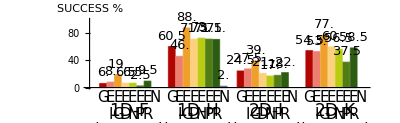

```mathematica
selectedData=selectData[sortedData,{"ID"->{"1D","2D"}}];
selectedData=removeData[selectedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}]; (* Removed 2D-J *)
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-1.2,-8}]};
padding={{40,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"1D-F"},{"(0,1,0,1)"}}],Grid[{{"1D-H"},{"(0,0,1,1)"}}],Grid[{{"2D-I"},{"(0,0,1,1)"}}],Grid[{{"2D-K"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_1d_2d.eps",%];
```

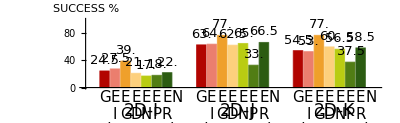

```mathematica
selectedData=selectData[sortedData,{"ID"->{"2D"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.5,-8}]};
padding={{30,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"2D-I"},{"(0,0,1,1)"}}],Grid[{{"2D-J"},{"(0,0,1,1)"}}],Grid[{{"2D-K"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
```

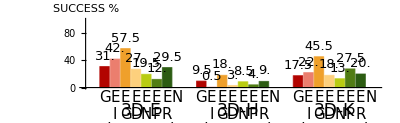

```mathematica
selectedData=selectData[sortedData,{"ID"->{"3D"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.5,-8}]};
padding={{30,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"3D-E"},{"(0,0,1,2)"}}],Grid[{{"3D-H"},{"(0,0,1,1)"}}],Grid[{{"3D-K"},{"(0,0,0,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_3d.eps",%];
```

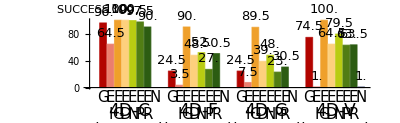

```mathematica
selectedData=selectData[sortedData,{"ID"->{"4D"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-1.2,-8}]};
padding={{40,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"4D-C"},{"(0,0,1,1)"}}],Grid[{{"4D-F"},{"(0,1,0,1)"}}],Grid[{{"4D-G"},{"(0,1,0,1)"}}],Grid[{{"4D-V"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_4d.eps",%];
```

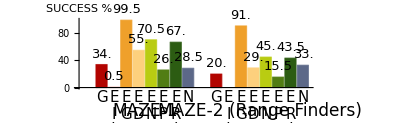

```mathematica
selectedData=selectData[sortedData,{"ID"->{"MAZE"}}];
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.0,-8}]};
padding={{30,0},{80,25}};
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"MAZE-1"},{"(0,1,1,0)"}}],Grid[{{"MAZE-2 (Range Finders)"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_maze.eps",%];
```

## Hyper Experiments All Comparison

```mathematica
names={"HNEAT_GECCO","HGP","HGP_GPEFS_NOGENERAL_GECCO","HGP_GPEFS_GENERAL_BEST_GECCO","ROBO_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
epilog={Text[Style[Grid[{{"Algorithm"},{"Distance"}},Alignment->{{Right},{Right}},Spacings->{2,0}],Background->White,Bold,FontSize->15],{-0.5,-8}]};
padding={{30,0},{80,25}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
solverRewrite,
distanceRewrite
}];
newLabels=ReplaceAll[newLabels,{{"G",""}->{"T",""},{"G",x:_}->{"E",x}}];
newLabels=ReplaceAll[newLabels,{{"T",""}->{"G",""}}];
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GP.DISTANCE","RECO.GENERATOR","PROBLEM"}];
```

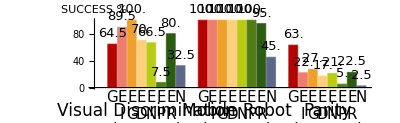

```mathematica
selectedData=selectData[sortedData,{"ID"->{"XOR","FC","ROBO"}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"Visual Discrimination"},{"(0,0,0,2)"}}],Grid[{{"Mobile Robot"},{"(0,1,0,1)"}}],Grid[{{"Parity"},{"(0,1,1,1)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_fc_robo_xor.eps",%];
```

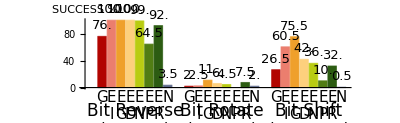

```mathematica
selectedData=selectData[sortedData,{"ID"->{"RECO1D"}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{Grid[{{"Bit Reverse"},{"(0,0,0,2)"}}],Grid[{{"Bit Rotate"},{"(1,0,0,1)"}}],Grid[{{"Bit Shift"},{"(0,0,0,10)"}}]},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_all_reco.eps",%];
```

## Normal Experiments General Detailed Comparison

```mathematica
names={"GP_GPEFS_GENERAL_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
epilog={Text[Style[Grid[{{"C"},{"α"},{"β"}},Spacings->{2,0}],Bold,FontSize->15],{0.7,-11}]};
padding={{30,0},{75,30}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","SYMBOLIC_REGRESSION.F","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
{"GP.DISTANCE_GENERAL_C",{"."->""}},
{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"false"->"0","true"->"1"}},
{"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"false"->"0","true"->"1"}}
}];
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_C","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","PROBLEM"}];
```

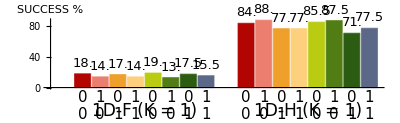

```mathematica
selectedData=selectData[sortedData,{"ID"->{"1D"},"GP.DISTANCE_GENERAL_K"->{1.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"1D-F (K = 1)","1D-H (K = 1)"},0.0,8]
```

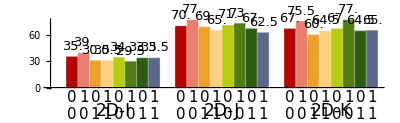

```mathematica
selectedData=selectData[sortedData,{"ID"->{"2D"},"GP.DISTANCE_GENERAL_K"->{1.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"2D-I","2D-J","2D-K"},0.0,8]
```

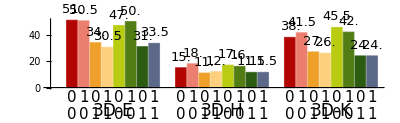

```mathematica
selectedData=selectData[sortedData,{"ID"->{"3D"},"GP.DISTANCE_GENERAL_K"->{1.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"3D-E","3D-H","3D-K"},0.0,8]
```

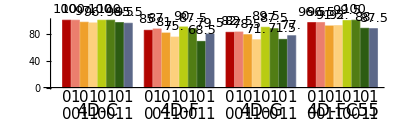

```mathematica
selectedData=selectData[sortedData,{"ID"->{"4D"},"GP.DISTANCE_GENERAL_K"->{1.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"4D-C","4D-F","4D-G","4D-FC55"},0.0,8]
```

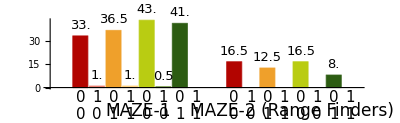

```mathematica
selectedData=selectData[sortedData,{"ID"->{"MAZE"},"GP.DISTANCE_GENERAL_K"->{10.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"MAZE-1","MAZE-2 (Range Finders)"},0.0,8]
```

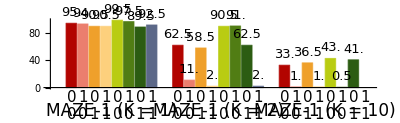

```mathematica
selectedData=selectData[sortedData,{"ID"->{"MAZE"},"MAZE.MAP"->"map2.csv","GP.DISTANCE_GENERAL_K"->{1.,2.,10.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"MAZE-1 (K = 1)","MAZE-1 (K = 2)","MAZE-1 (K = 10)"},0.0,8]
```

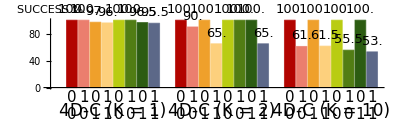

```mathematica
selectedData=selectData[sortedData,{"ID"->{"4D"},"SYMBOLIC_REGRESSION.F"->"C","GP.DISTANCE_GENERAL_K"->{1.,2.,10.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"4D-C (K = 1)","4D-C (K = 2)","4D-C (K = 10)"},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_general_4d_C_for_K.eps",%];
```

### All Results

```mathematica
printGeneralizedMeasure[list_]:=
Module[{plot},
selectedData=selectData[sortedData,{"ID"->{list[[1]]},"GP.DISTANCE_GENERAL_K"->{1.,2.,10.}}~Join~If[Length[list]>3,list[[4]],{}]];
plot=plotBooleanAsBarChartPub[selectedData,"SUCCESS",(list[[2]]<>" "<>#)&/@{"(K = 1)","(K =2)","(K =10)"},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding];
Export["gecco2012_general_"<>list[[3]]<>"_for_K.eps",plot];
plot
]
```

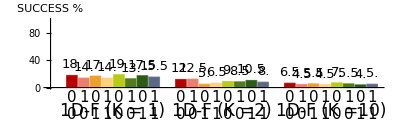
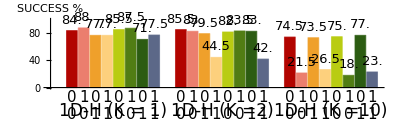
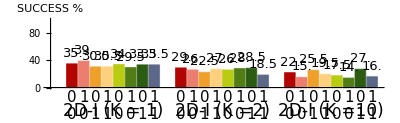
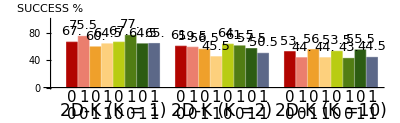
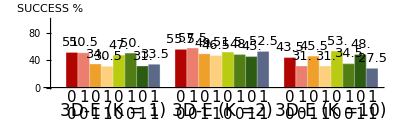
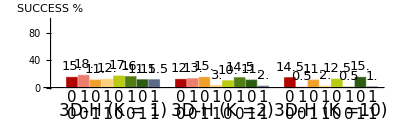
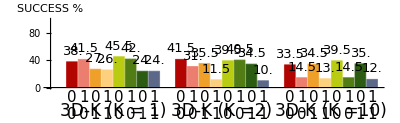
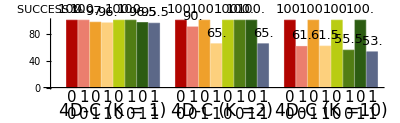

```mathematica
printGeneralizedMeasure[#]&/@{
{"1D","1D-F","1df",{"SYMBOLIC_REGRESSION.F"->"F"}},
{"1D","1D-H","1dh",{"SYMBOLIC_REGRESSION.F"->"H"}},
{"2D","2D-I","2di",{"SYMBOLIC_REGRESSION.F"->"I"}},
{"2D","2D-K","2dk",{"SYMBOLIC_REGRESSION.F"->"K"}},
{"3D","3D-E","3de",{"SYMBOLIC_REGRESSION.F"->"E"}},
{"3D","3D-H","3dh",{"SYMBOLIC_REGRESSION.F"->"H"}},
{"3D","3D-K","3dk",{"SYMBOLIC_REGRESSION.F"->"K"}},
{"4D","4D-C","4dc",{"SYMBOLIC_REGRESSION.F"->"C"}},
{"4D","4D-F","4df",{"SYMBOLIC_REGRESSION.F"->"F"}},
{"4D","4D-G","4dg",{"SYMBOLIC_REGRESSION.F"->"G"}},
{"4D","4D-V","4dv",{"SYMBOLIC_REGRESSION.F"->"ZFC55"}},
{"MAZE","MAZE-1","maze1",{"MAZE.MAP"->"map2.csv"}},
{"MAZE","MAZE-2","maze2",{"MAZE.MAP"->"map4.csv"}}
}
```

## Hyper Experiments General Detailed Comparison

```mathematica
names={"HGP_GPEFS_GENERAL_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
epilog={Text[Style[Grid[{{"C"},{"α"},{"β"}},Spacings->{2,0}],Bold,FontSize->15],{0.7,-11}]};
padding={{30,0},{75,30}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","RECO.GENERATOR","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
{"GP.DISTANCE_GENERAL_C",{"."->""}},
{"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"false"->"0","true"->"1"}},
{"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"false"->"0","true"->"1"}}
}];
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_C","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","PROBLEM"}];
```

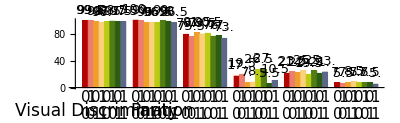

```mathematica
selectedData=selectData[sortedData,{"ID"->{"FC","XOR"},"GP.DISTANCE_GENERAL_K"->{1.,2.,10.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"Visual Discrimination","Parity"},0.0,8]
```

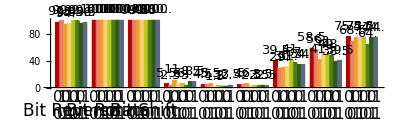

```mathematica
selectedData=selectData[sortedData,{"ID"->{"RECO1D"},"GP.DISTANCE_GENERAL_K"->{1.,2.,10.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"Bit Reverse","Bit Rotate","Bit Shift"},0.0,8]
```

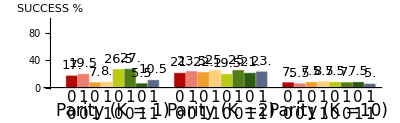

```mathematica
selectedData=selectData[sortedData,{"ID"->{"XOR"},"GP.DISTANCE_GENERAL_K"->{1.,2.,10.}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"Parity (K = 1)","Parity (K =2)","Parity (K =10)"},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_general_xor_for_K.eps",%];
```

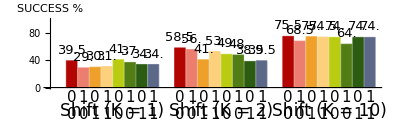

```mathematica
selectedData=selectData[sortedData,{"ID"->{"RECO1D"},"GP.DISTANCE_GENERAL_K"->{1.,2.,10.},"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D"}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"Shift (K = 1)","Shift (K = 2)", "Shift (K = 10)"},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
(*Export["gecco2012_general_reco_for_K.eps",%];*)
```

### All Results

```mathematica
Clear[printGeneralizedMeasure]
```

```mathematica
printGeneralizedMeasure[list_]:=
Module[{plot},
selectedData=selectData[sortedData,{"ID"->{list[[1]]},"GP.DISTANCE_GENERAL_K"->{1.,2.,10.}}~Join~If[Length[list]>3,list[[4]],{}]];
plot=plotBooleanAsBarChartPub[selectedData,"SUCCESS",(list[[2]]<>" "<>#)&/@{"(K = 1)","(K =2)","(K =10)"},0.0,8,Epilog->epilog,PlotRange->plotRange,ImagePadding->padding];
Export["gecco2012_general_"<>list[[3]]<>"_for_K.eps",plot];
plot
]
```

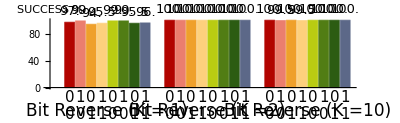
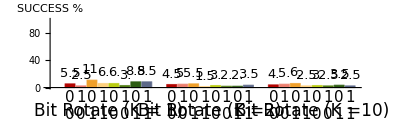
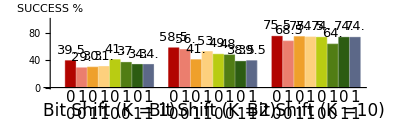
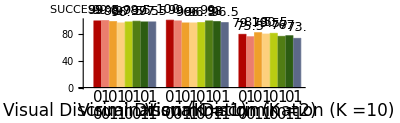
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
printGeneralizedMeasure[#]&/@{
{"RECO1D","Bit Reverse","reco_reverse",{"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D"}}},
{"RECO1D","Bit Rotate","reco_rotate",{"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D"}}},
{"RECO1D","Bit Shift","reco_shift",{"RECO.GENERATOR"->{"hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D"}}},
{"FC","Visual Discrimination","fc"},
{"XOR","Parity","xor"}
}
```

## Normal Experiments General Aggregated K Comparison

```mathematica
names={"GP_GPEFS_GENERAL_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
epilog={Text[Style[Grid[{{"K"}},Spacings->{2,0}],Bold,FontSize->15],{0.7,-5}]};
padding={{30,0},{75,25}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","SYMBOLIC_REGRESSION.F","SOLVER","GP.DISTANCE"}];
aggregatedKData=aggregateBoolean[sortedData,"SUCCESS",8];
newLabels=extractParameters[aggregatedKData,{
{"GP.DISTANCE_GENERAL_K",{"."->""}}
}];
aggregatedKData=replaceLabels[aggregatedKData,newLabels];
printAsTable[aggregatedKData,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_C","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","PROBLEM"}];
```

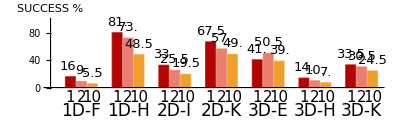

```mathematica
selectedData=selectData[aggregatedKData,{"ID"->{"1D","2D","3D"}}];
selectedData=removeData[selectedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}]; (* Removed 2D-J *)
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"1D-F","1D-H","2D-I","2D-K","3D-E","3D-H","3D-K"},0.0,3,Operation->(Round[100*Mean[#],0.5]&),Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_general_1d_2d_3d_for_aggregated_K.eps",%];
```

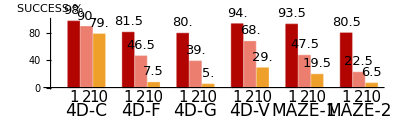

```mathematica
selectedData=selectData[aggregatedKData,{"ID"->{"4D","MAZE"}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"4D-C","4D-F","4D-G","4D-V","MAZE-1","MAZE-2"},0.0,3,Operation->(Round[100*Mean[#],0.5]&),Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_general_4d_maze_for_aggregated_K.eps",%];
```

## Hyper Experiments General Aggregated K Comparison

```mathematica
names={"HGP_GPEFS_GENERAL_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
epilog={Text[Style[Grid[{{"K"}},Spacings->{2,0}],Bold,FontSize->15],{0.7,-5}]};
padding={{30,0},{75,20}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","RECO.GENERATOR","SOLVER","GP.DISTANCE"}];
aggregatedKData=aggregateBoolean[sortedData,"SUCCESS",8];
newLabels=extractParameters[aggregatedKData,{
{"GP.DISTANCE_GENERAL_K",{"."->""}}
}];
aggregatedKData=replaceLabels[aggregatedKData,newLabels];
printAsTable[aggregatedKData,{"SOLVER","ID","RECO.GENERATOR","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_C","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","PROBLEM"}];
```

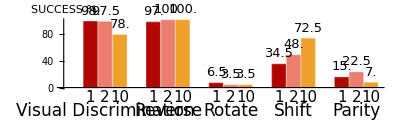

```mathematica
plotBooleanAsBarChartPub[aggregatedKData,"SUCCESS",{"Visual Discrimination","Reverse","Rotate","Shift","Parity"},0.0,3,Operation->(Round[100*Mean[#],0.5]&),Epilog->epilog,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_general_hyper_for_aggregated_K.eps",%];
```

## Normal Experiments NEAT Config Comparison

```mathematica
names={"NEAT_GECCO","NEAT_G2000_GECCO","NEAT_P200_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55","NONE"->"ANONE"}];
```

```mathematica
changingParameters[data]
```

{GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GP.TARGET_FITNESS,ID,MAZE.MAP,NEAT.maxGenerations,NEAT.populationSize,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
epilog={Text[Style[Grid[{{"VERSION"}},Spacings->{2,0}],Bold,FontSize->15],{-3,-5}]};
padding={{30,0},{75,20}};
sortedData = sortDataByParams[data,{"ID","PROBLEM","SYMBOLIC_REGRESSION.F","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
{"NEAT.maxGenerations",{}},
{"NEAT.populationSize",{}}
}];
newLabels=newLabels/.{{"1000","100"}->{"B"},{"2000","100"}->{"G"},{"1000","200"}->{"P"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","NEAT.maxGenerations","NEAT.populationSize","PROBLEM"}];
```

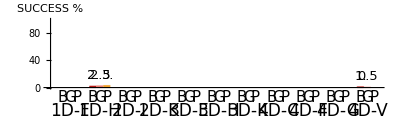

```mathematica
selectedData=selectData[sortedData,{"ID"->{"1D","2D","3D","4D"}}];
selectedData=removeData[selectedData,{"SYMBOLIC_REGRESSION.F"->{"J"}}]; (* Removed 2D-J *)
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"1D-F","1D-H","2D-I","2D-K","3D-E","3D-H","3D-K","4D-C","4D-F","4D-G","4D-V"},0.0,3,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_neats_sr.eps",%];
```

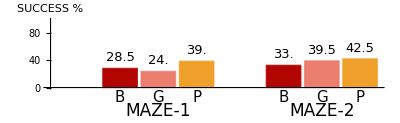

```mathematica
selectedData=selectData[sortedData,{"ID"->{"MAZE"}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"MAZE-1","MAZE-2"},0.0,3,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_neats_maze.eps",%];
```

```mathematica
fcomp={2*31,2*39.5};
testFisherExact[{{fcomp[[1]],200-fcomp[[1]]},{fcomp[[2]],200-fcomp[[2]]}}]
```

0.0938587

## Hyper Experiments NEAT Config Comparison

```mathematica
names={"HNEAT_GECCO","HNEAT_G2000_GECCO","HNEAT_P200_GECCO"};
data=readAllFiles[names,Null,ReplaceParamValues->{"RECO1D"->"ARECO1D"}];
```

```mathematica
epilog={Text[Style[Grid[{{"VERSION"}},Spacings->{2,0}],Bold,FontSize->15],{-3,-5}]};
padding={{30,0},{75,20}};
sortedData = sortDataByParams[data,{"ID","RECO.GENERATOR","SOLVER","GP.DISTANCE"}];
newLabels=extractParameters[sortedData,{
{"NEAT.maxGenerations",{}},
{"NEAT.populationSize",{}}
}];
newLabels=newLabels/.{{"1000","100"}->{"B"},{"2000","100"}->{"G"},{"1000","200"}->{"P"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GP.DISTANCE","RECO.GENERATOR","NEAT.maxGenerations","NEAT.populationSize","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | ID | GP.DISTANCE | RECO.GENERATOR | NEAT.maxGenerations | NEAT.populationSize | PROBLEM
{B} | HNEAT_GECCO/parameters_002.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 1000 | 100 | RECO
{G} | HNEAT_G2000_GECCO/parameters_002.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 2000 | 100 | RECO
{P} | HNEAT_P200_GECCO/parameters_002.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | 1000 | 200 | RECO
{B} | HNEAT_GECCO/parameters_004.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 1000 | 100 | RECO
{G} | HNEAT_G2000_GECCO/parameters_004.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 2000 | 100 | RECO
{P} | HNEAT_P200_GECCO/parameters_004.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | 1000 | 200 | RECO
{B} | HNEAT_GECCO/parameters_003.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 1000 | 100 | RECO
{G} | HNEAT_G2000_GECCO/parameters_003.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 2000 | 100 | RECO
{P} | HNEAT_P200_GECCO/parameters_003.txt | NEAT | ARECO1D |  | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | 1000 | 200 | RECO
{B} | HNEAT_GECCO/parameters_001.txt | NEAT | FC |  |  | 1000 | 100 | FIND_CLUSTER
{G} | HNEAT_G2000_GECCO/parameters_001.txt | NEAT | FC |  |  | 2000 | 100 | FIND_CLUSTER
{P} | HNEAT_P200_GECCO/parameters_001.txt | NEAT | FC |  |  | 1000 | 200 | FIND_CLUSTER
{B} | HNEAT_GECCO/parameters_005.txt | NEAT | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR | 1000 | 100 | XOR
{G} | HNEAT_G2000_GECCO/parameters_005.txt | NEAT | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR | 2000 | 100 | XOR
{P} | HNEAT_P200_GECCO/parameters_005.txt | NEAT | XOR |  | hyper.experiments.reco.problem.PatternGeneratorXOR | 1000 | 200 | XOR

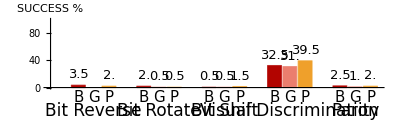

```mathematica
selectedData=selectData[sortedData,{"ID"->{"ARECO1D","FC","XOR"}}];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",{"Bit Reverse","Bit Rotate","Bit Shift","Visual Discrimination","Parity"},0.0,3,PlotRange->plotRange,ImagePadding->padding]
Export["gecco2012_neats_indirect.eps",%];
```

## VIVAE BSF

```mathematica
Needs["PlotLegends`"]
readRunFitness[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
readRunEvaluationInfo[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
data = Rest[allData];
{data,Max/@data, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
enlarge[list_, fill_, stat_]:=list~Join~Array[fill&,Max[Length/@stat]-Length[list]]
enlarge[list_, fill_, stat_, len_]:=list~Join~Array[fill&,len-Length[list]]
enlarge[list_,bsfAvg_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
bsfAvgGP = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_GP_GECCO"}]);
bsfAvgBASIC = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_BASIC_GECCO"}]);
bsfAvgGENERAL = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_GENERAL_GECCO"}]);
bsfAvgISO = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_ISO_GECCO"}]);
bsfAvgNODES = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_NODES_GECCO"}]);
bsfAvgPHENO = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_PHENO_GECCO"}]);
bsfAvgRANDOM = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HGP_robo_RANDOM_GECCO"}]);
bsfAvgNEAT = (readRunFitness[#]⟦2⟧&/@FileNames["run_001*FITNESS.txt",{"~/java/exp/HNEAT_robo_NEAT_GECCO"}]);
```

```mathematica
maxGenerations=Max@@(Max[Length[#]&/@#]&/@{bsfAvgGP,bsfAvgBASIC,bsfAvgGENERAL,bsfAvgISO,bsfAvgNODES,bsfAvgPHENO,bsfAvgRANDOM,bsfAvgNEAT})
```

50

```mathematica
bsfAvgGP=Mean[(enlarge/@bsfAvgGP)];
bsfAvgBASIC=Mean[(enlarge/@bsfAvgBASIC)];
bsfAvgGENERAL=Mean[(enlarge/@bsfAvgGENERAL)];
bsfAvgISO=Mean[(enlarge/@bsfAvgISO)];
bsfAvgNODES=Mean[(enlarge/@bsfAvgNODES)];
bsfAvgPHENO=Mean[(enlarge/@bsfAvgPHENO)];
bsfAvgRANDOM=Mean[(enlarge/@bsfAvgRANDOM)];
bsfAvgNEAT=Mean[(enlarge/@bsfAvgNEAT)];
```

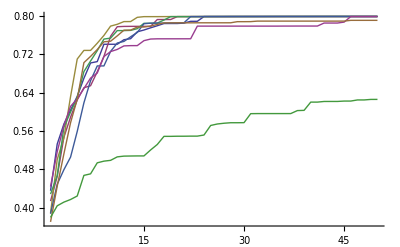

```mathematica
ListLinePlot[{bsfAvgGP,bsfAvgBASIC,bsfAvgGENERAL,bsfAvgISO,bsfAvgNODES,bsfAvgPHENO,bsfAvgRANDOM,bsfAvgNEAT}, PlotRange->All]
```

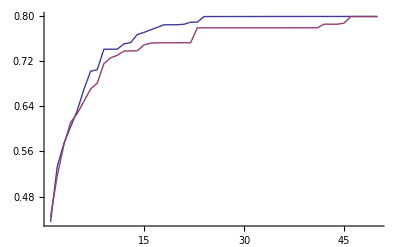

```mathematica
ListLinePlot[{bsfAvgGP,bsfAvgPHENO}, PlotRange->All]
```